# Comp Bio Homework 1

## Problem 1 : Time delayed model with Allee effect

## a) Show examples of the different dynamics obtained in this model :

Allee  effect  model 
-Graphics-

- no oscillations
- damped oscillations
- stable oscillations

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of NDSolveValue::ihist will be suppressed during this calculation.

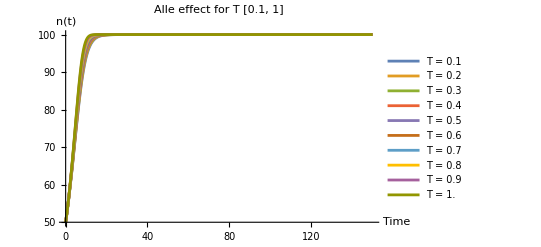

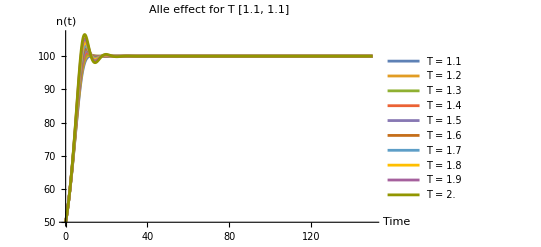

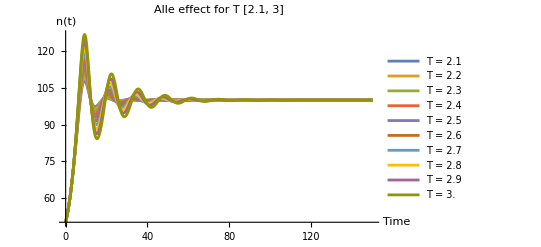

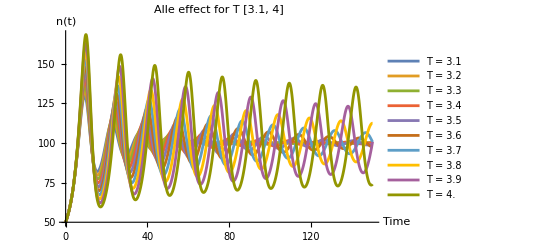

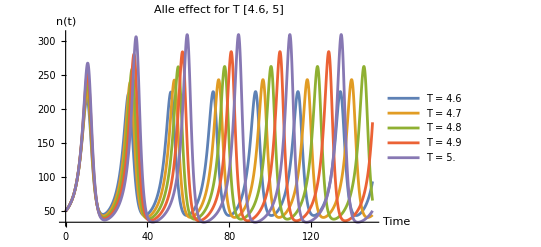

```mathematica
ClearAll["Global`*"];

(*Define parameters*)
A=20;
K=100;
r=0.1;

(* Determine T values*)
TValues = Range[0.1,5,0.1];

t0 = 0;
tMax = 150;

(*Initial condition*)
initCond = n[0] == 50;

(*Solve diff equation*)
solveDifferentialEquation[T_] := NDSolveValue[
	{n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1), initCond}, 
    n, {t, t0, tMax}
];

(* solutions for differen T*)
solutions = Table[
	solveDifferentialEquation[T], 
	{T, TValues}
];

legends = {
	"T = 1, no oscillations", 
	"T = 3, damped oscillations", 
	"T = 5, stable oscillations (limit cycles)"
};

colors = {
	Red,
	Green,
	Blue
};

Plot[Evaluate[Table[solutions[[i]][t], {i, 1,10}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 1,10}], 
     PlotLabel -> "Alle effect for T [0.1, 1]", 
     AxesLabel -> {"Time", "n(t)"}

]

Plot[Evaluate[Table[solutions[[i]][t], {i, 11,20}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 11, 20}], 
     PlotLabel -> "Alle effect for T [1.1, 1.1]", 
     AxesLabel -> {"Time", "n(t)"}
]

Plot[Evaluate[Table[solutions[[i]][t], {i, 21,30}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 21, 30}], 
     PlotLabel -> "Alle effect for T [2.1, 3]", 
     AxesLabel -> {"Time", "n(t)"}
]

Plot[Evaluate[Table[solutions[[i]][t], {i, 31,40}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 31, 40}], 
     PlotLabel -> "Alle effect for T [3.1, 4]", 
     AxesLabel -> {"Time", "n(t)"}
]

Plot[Evaluate[Table[solutions[[i]][t], {i, 46,50}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 46, 50}], 
     PlotLabel -> "Alle effect for T [4.6, 5]", 
     AxesLabel -> {"Time", "n(t)"}
]
```

The fives plots each contain the trajectories for different T values. One find that in the case of T small [0.1, 1], there is no osciallation at all. At the value T = 1.1 we slowly see an overshoot, which after a couple of periods is damped completely and goes into a steady state a N = 100. 
In the range T = [3.1, 4] one still observes a dampened behaviour, the oscillation is still exisiting at t = 150, but we see it is enclosed by a shrinking behaviour.
At T = 4.6 one can find an purely oscillating behaviour which is not dampened.

## b) Estimate numerically with one decimal precision the value T at which the dynamics starts exhibiting damped oscillations

As described before, at T = 1.1 a first overshoot can be observed. As this trajectory goes into steady state for longer t, here the first damped oscillation can be observed.
For this lets look at the dyanamics for T = 0.9, 1, 1.1 closer

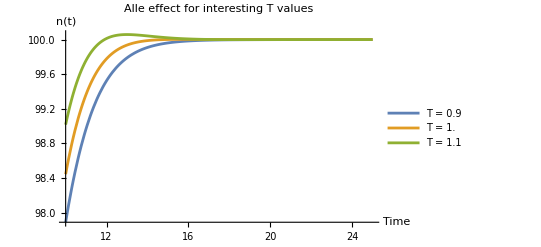

```mathematica
Plot[Evaluate[Table[solutions[[i]][t], {i, 9,11}]], {t, 10, 25},
     PlotRange -> All, 
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 9, 11}],
     PlotLabel -> "Alle effect for interesting T values", 
     AxesLabel -> {"Time", "n(t)"}
]
```

## c) Estimate numerically with one decimal precision the value of T (denoted by TH) at which a bifurcation (Hopf bifurcation) occurs .

A Hopf Bifurcation has happened when periodic solutions arise, namely when a spiral and a limit cycle collide. From the observation in subtask a) we know the interesting behaviour lays in the area around T = 4.5. So lets check a couple of trajectories there

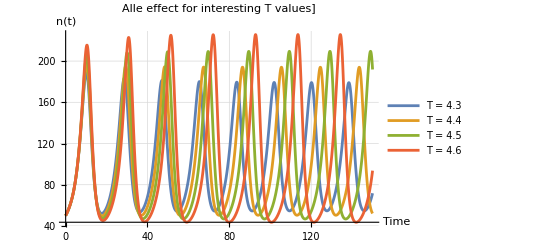

```mathematica
Plot[Evaluate[Table[solutions[[i]][t], {i, 43,46}]], {t, t0, 150},
     PlotRange -> All, 
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 43, 46}],
     PlotLabel -> "Alle effect for interesting T values]", 
     AxesLabel -> {"Time", "n(t)"},
     GridLines->Automatic
]
```

For the trajectory of T = 4.3 one finds a still dampened oscillation. For the trajectory of T = 4.4, we find that there is no increase nor shrinking of the trajectory going on. Very good visible on the grid line of n(t) = 50. For the 2 trajectories T = 4.5 and T = 4.6 we find also perfectly repeating trajectories, they lie on a limit cycle. So the Hopf Bifurcation happens at T = 4.4.

## d) Use linear stability analysis to analytically compute the value of T_H. Do this by linearising Eq.(1) around the steady state N* = K and use a pertubation that is proportional to exp(λt). Compare T_H that you obtain analytically to the estimate found in c). Discuss the result.

To find the point of T_H we need to investigate the real part of the eigenvalues of the system. As soon as the sign of the real part of the eigenvalues are changing the Hopf Bifurcation happens.

```mathematica
ClearAll["Global`*"];

(*Define parameters*)
A=20;
K=100;
r=0.1;

(*Determine T values*)
TValues=Range[0.1,5,0.1];

t0=0;
tMax=150;

(*Initial condition*)
initCond=n[0]==50;

(*Define equilibrium point*)
n_eq=K;

(*Define a small perturbation ε*)
e=0.01;

(* define the function *)
nPrime[t_] := r*n[t]*(1-n[t-T]/K)*(n[t]/A-1);

nDoublePrime[†_] = D[nPrime[t], t]

nLin[t_] := nDoublePrime[t]

(*
fLin[n_] := fPrime[K] * (n - K);


Plot[fLin[n[t]], {n[t], 0, 200}]
*)

(*Linearized differential equation*)
(*
linearizedDE=Series[ r*n[t]*(1-n[t-T]/K)*(n[t]/A-1) ,{n,n_eq,0}];
linearizedDE = Normal[linearizedDE]*)
(*
(*Solve linearized equation*)
linearizedSolution=NDSolveValue[{n'[t]==linearizedDE,n[0]==n_eq+e},n,{t,t0,tMax}];

(*Plot the linearized solution*)
Plot[linearizedSolution[t],{t,t0,tMax},PlotLabel->"Linearized Solution for e = "<>ToString[ε],AxesLabel->{"Time","n(t)"}]




*)
```

0.1 (-1+n[t]/20) (1-1/100 n[t-T]) n'[t]+0.005 n[t] (1-1/100 n[t-T]) n'[t]-0.001 (-1+n[t]/20) n[t] n'[t-T]

```mathematica
ClearAll["Global`*"];

(* Define the original differential equation *)
originalEq = n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1);

(* Define the scales for variables and parameters *)
(* These are illustrative; you should choose scales relevant to your problem *)
timeScale = tScale * tStar;  (* tScale is the scale for time *)
nScale = nStar * n0;  (* n0 is the scale for n(t) *)
rScale = rStar * r0;  (* r0 is the scale for r *)
TScale = TStar * tScale;  (* Non-dimensionalize T with time scale *)
KScale = KStar * n0;  (* Non-dimensionalize K with n scale *)
AScale = AStar * n0;  (* Non-dimensionalize A with n scale *)

(* Apply NondimensionalizationTransform *)
scales = {t -> timeScale, n[t] -> nScale, r -> rScale, T -> TScale, K -> KScale, A -> AScale};
nondimensionalEq = NondimensionalizationTransform[originalEq, {t, n[t]}, {tStar, nStar}, scales];

(* Display the nondimensional equation *)
nondimensionalEq
```

NondimensionalizationTransform::invpq1: Original variables supplied include unrecognized physical quantities.

NondimensionalizationTransform[n'[t]==r n[t] (-1+n[t]/A) (1-1/100 n[t-T]),{t,n[t]},{tStar,nStar},{t→tScale tStar,n[t]→n0 nStar,r→r0 rStar,T→tScale TStar,100→KStar n0,A→AStar n0}]